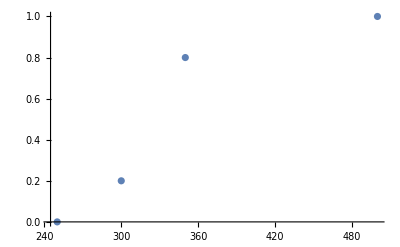

```mathematica
A={{250, 0},{300, 0.2},{350, 0.8}, {500, 1}};
ListPlot[A]
```

```mathematica
approx=Fit[A,{1,x^2},x]
```

-0.159236+5.02275×10^-6 x^2

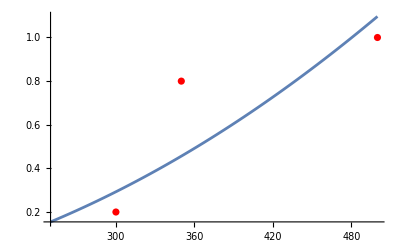

```mathematica
Show[Plot[approx,{x,250, 500}],ListPlot[A,PlotStyle->Red]]
```